-(ⅈ Rl)/(-ⅈ (Rl+Rs)+(L+C1 Rl Rs) ω+ⅈ C1 L Rl ω^2)

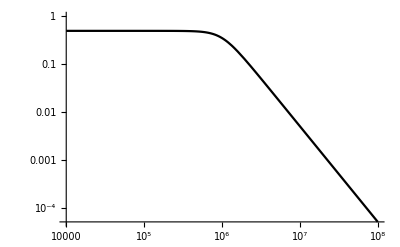

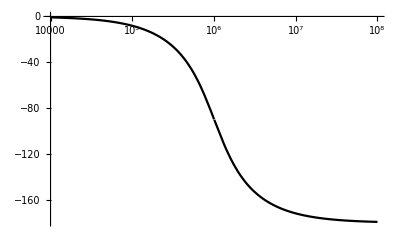

```mathematica
ClearAll[Rs,Rl,L,C1];
$Assumptions=Rs>0&&Rl>0&&L>0&&C1>0;
Par[x_,y_]:=x*y/(x+y);
XX[ω_]:=Par[Rl,1/(ⅈ*ω*C1)];
A[ω_]:=XX[ω]/(Rs+ⅈ*ω*L+XX[ω]);
FullSimplify[A[ω]]
Rs=50;Rl=50;L=10*10^-6;C1=5*10^-9;
xTicks={0.01,0.1,1,10,100,10^3,10^4};
afTicks={xTicks,{0.0001,0.001,0.01,0.1,1}};
af=LogLogPlot[Abs[A[2 π f]],{f,10000,100000000},PlotTheme->"Monochrome"]
pfTicks={xTicks,{90,75,60,45,30,15,0}};
pf=LogLinearPlot[Arg[A[2 π f]]*180/π,{f,10000,100000000},PlotTheme->"Monochrome"]
```

```mathematica
ClearAll[Rs,Rl,L,C1];
Ω=ω/√((Rs+Rl)/(L C1 Rl));ζ=((√(L/C1))/(2 Rl)+(Rs √(C1/L))/2)√(Rl/(Rs+Rl));
FullSimplify[(Rl/(Rs+Rl))/(1+2 ⅈ ζ Ω-Ω^2)]
```

Rl/(Rl+Rs+ⅈ (L+C1 Rl Rs) ω-C1 L Rl ω^2)

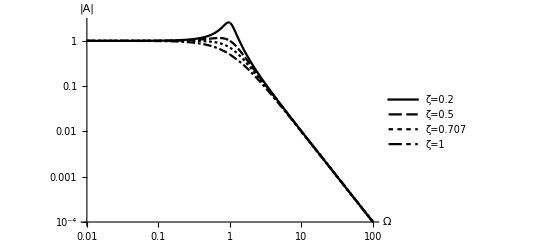

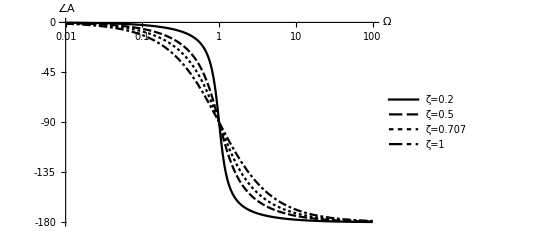

```mathematica
G[Ω_,ζ_]:=1/(1+2 ⅈ ζ Ω-Ω^2);
ζ={0.2,0.5,1/√2,1};
LogLogPlot[{Abs[G[o,ζ[[1]]]],Abs[G[o,ζ[[2]]]],Abs[G[o,ζ[[3]]]],Abs[G[o,ζ[[4]]]]},
{o,0.01,100},PlotTheme->"Monochrome",AxesLabel->{"Ω","|A|"},PlotLegends->{"ζ=0.2","ζ=0.5","ζ=0.707","ζ=1"}]
LogLinearPlot[{Arg[G[o,ζ[[1]]]]*180/π,Arg[G[o,ζ[[2]]]]*180/π,Arg[G[o,ζ[[3]]]]*180/π,Arg[G[o,ζ[[4]]]]*180/π},
{o,0.01,100},PlotTheme->"Monochrome",Ticks->{Automatic,{0,-45,-90,-135,-180}},AxesLabel->{"Ω","∠A"},PlotLegends->{"ζ=0.2","ζ=0.5","ζ=0.707","ζ=1"}]
```

```mathematica
ClearAll[Rs,Rl,L,C1,ω0,ζ];
$Assumptions=Rs>0&&Rl>0&&L>0&&C1>0;
(*ζ=1/√2;*)
Solve[{√((Rs+Rl)/(L C1 Rl))==ω0,1/(√2)==((√(L/C1))/(2 Rl)+(Rs √(C1/L))/2)√(Rl/(Rs+Rl))},{L,C1}]
```

$Aborted